```mathematica
Head[{1, 2, 3, 5}]
```

List

```mathematica
AtomQ[x32]
```

True

```mathematica
FullForm[{a, b, c}]
```

List[a,b,c]

```mathematica
Part[a+b,1]
```

a

```mathematica
Head[a+b]
```

Plus

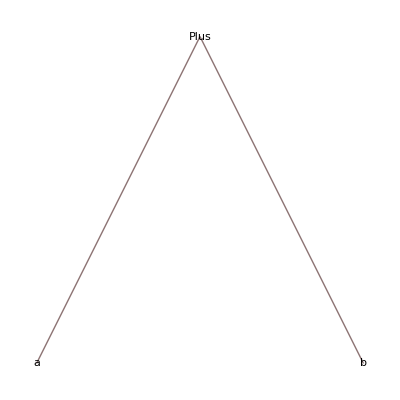

```mathematica
TreeForm[a+b]
```

```mathematica
(3+4ⅈ)[[1]]
```

Part::partd: Part specification (3 + 4\ ⅈ) ⟦ 1 ⟧ is longer than depth of object.

(3+4 ⅈ)⟦1⟧

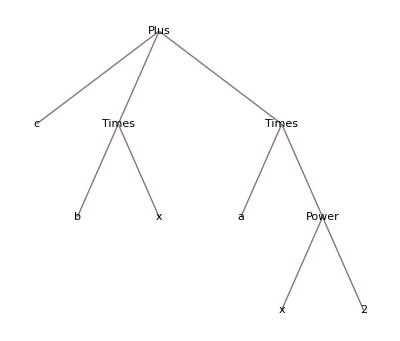

```mathematica
TreeForm[a x^2+b x + c]
```

```mathematica
(a x^2+b x + c)[[1]]
```

c

```mathematica
(a x^2+b x + c)[[2,1]]
```

b

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Table[i^2,{i,1,5}]
```

{1,4,9,16,25}



```mathematica
Plot[Sin[x],{x,0,2π}]
```

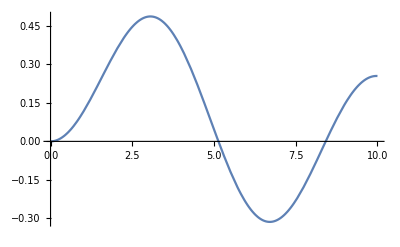
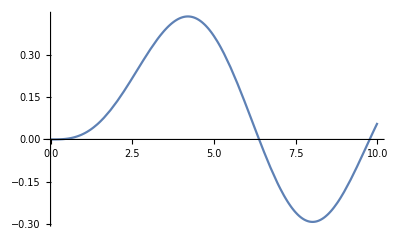
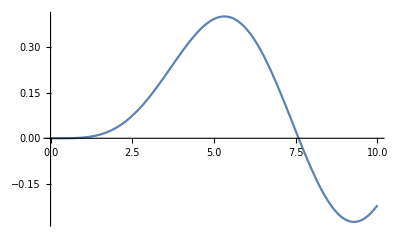
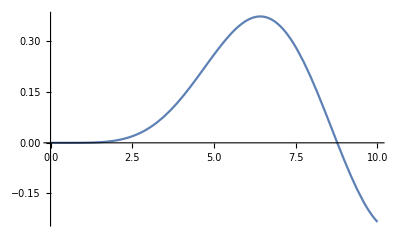

```mathematica
Table[Plot[BesselJ[n,x],{x,0,10}],{n,2,5}]
```

```mathematica
vec = {2, 3, 7, 8, 1, 4}
vec[[2,4]]
```

{2,3,7,8,1,4}

Part::partd: Part specification {2, 3, 7, 8, 1, 4} ⟦ 2, 4 ⟧ is longer than depth of object.

{2,3,7,8,1,4}⟦2,4⟧

```mathematica
mat = Table[Subscript[a, i,j],{i,3},{j,3}]
```

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)},{a_(3,1),a_(3,2),a_(3,3)}}

```mathematica
MatrixForm[mat]
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

```mathematica
MatchQ[Bob, _]
```

True

```mathematica
Cases[{g[x],f[x]},_g]
```

{g[x]}

```mathematica
FullForm[1/3]
```

Rational[1,3]

```mathematica
Cases[a x^4+ b x^3+ d x,(_)^_,Infinity]
```

{x^3,x^4}

```mathematica
MatchQ[{1, 2, 3, 4, 5},_List]
```

True

```mathematica
MatchQ[{1, 2, 3, 4, 5},{__?NumberQ}]
```

True

```mathematica
MatchQ[{1, 2, 3, 4, 5},{_?NumberQ}]
```

False

```mathematica
Cases[{1, 2, 3, 4, 5},{_?NumberQ}]
```

{}

```mathematica
Cases[{1, 2, 3, 4, 5},_?NumberQ]
```

{1,2,3,4,5}